```mathematica
getNthDigit[nthDigit_]:=N[FromDigits[{RealDigits[N[Sqrt[2], 50]][[1]][[1;;nthDigit+1]], 1}], 50]
```

## Square

```mathematica
x[n_]:=Sqrt[2 (1- Sqrt[1-x[n-1]^2/4])];
drawPlot[i_]:=Module[{},
x[1]=getNthDigit[i];
estimation=Table[x[k]2^(k-1) 2, {k, 1, 50}];
error=Pi-estimation;
logError=Log10[Abs[error]];
ListPlot[logError, PlotLabel->"log Error"i, PlotRange->{0, -25}]
]
```

## Triangle

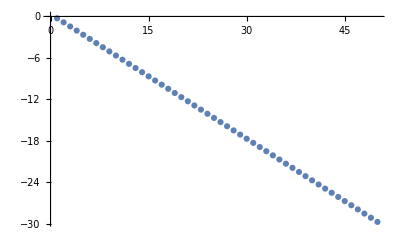

```mathematica
x[n_]:=Sqrt[2 (1- Sqrt[1-x[n-1]^2/4])];
precision=200; 
x[1]=N[Sqrt[3], precision];
estimation=Table[x[k]2^(k-1) 3/2, {k, 1, 50}];
error=Pi-estimation;
logError=Log10[Abs[error]];
ListPlot[logError]
```

## Practice

```mathematica
x[1]=1.4
```

1.4

```mathematica
x[2]
```

0.756118

```mathematica
i=10;
x[i]
```

0.0030289

```mathematica
x[11]
```

0.00151445

## digit and iteration plot

```mathematica
code[digit_, iter_]:=Module[{},
getNthDigit[nthDigit_]:=N[FromDigits[{RealDigits[N[Sqrt[2], 50]][[1]][[1;;nthDigit+1]], 1}], 50];
x[n_]:=Sqrt[2 (1- Sqrt[1-x[n-1]^2/4])];
xest[n_]:=Sqrt[2 (1- Sqrt[1-xest[n-1]^2/4])];
y[n_]:=2^n x[n];
yest[n_]:=2^n xest[n];
x[1]=Sqrt[2];
xest[1]=getNthDigit[digit];
error[n_]:=Pi-y[n];
errorest[n_]:=Pi-yest[n];
logerror[n_]:=Log10[Pi-y[n]];
logerrorest[n_]:=Log10[Pi-yest[n]];
relerror[n_]:=(x[n]-xest[n])/xest[n];
ListPlot[{Table[{i, logerror[i]},{i, 1, iter}],Table[{i, logerrorest[i]},{i, 1, iter}]}, PlotLegends->{"error", "error est"}, AxesLabel->{"n","log(e_n)"}]

]
```

```mathematica
(*Manipulate[code[i, j], {i, 1, 30, 1}, {j, 1, 50,1}]*)
```

```mathematica
fprime[x_]:=x/(2 √(4-x^2) √(2-√(4-x^2)));
```

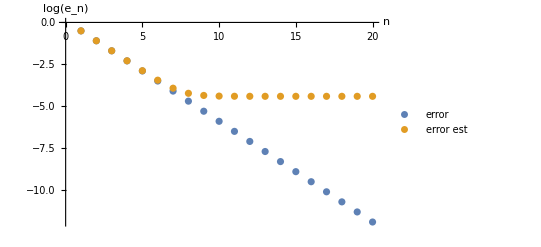

```mathematica
code[4, 20]
```

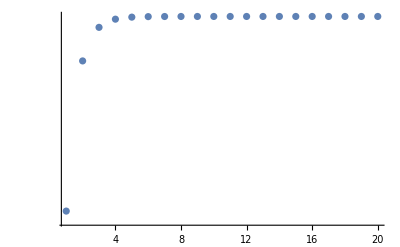

```mathematica
ListLogPlot[Table[errorest[i]-error[i], {i, 1, 20}], PlotRange->Full]
```

```mathematica
relerror[1]
```

4.41044404178023252671606501271340373114646×10^-8

```mathematica
relerror[10]//ScientificForm
```

5.61554730302760905201543225435237828687867×10^-8

```mathematica
Manipulate[y[i]-yest[i]//N, {i, 1, 20, 1}]
```

```mathematica
xest[1]
```

1.4142135

```mathematica
N[error[10]-errorest[10], 50]
```

-1.76417542436008369259601497551637339092414×10^-7

```mathematica
errorest[9]
```

5.1047295532823549979181793000705457140086691×10^-6

```mathematica
x[10]-xest[10]//N
```

1.72283×10^-10

```mathematica
xest[10]//ScientificForm
```

3.0679602002867749394429711954485707071388901930393×10^-3

```mathematica
relerror[10]
```

5.61554730302760905201543225435237828687867×10^-8

```mathematica
fprime[xest[9]]-0.5//ScientificForm
```

1.76483×10^-6

```mathematica
error[9]//N
```

4.92831×10^-6

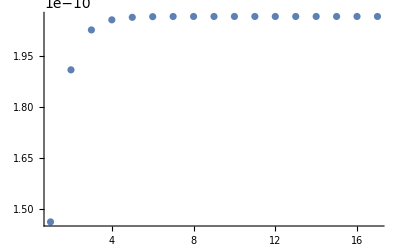

```mathematica
ListPlot[Table[N[(-error[i]+errorest[i]),50], {i, 1, 17}], PlotRange->All]
```

```mathematica
xest[3]/xest[4]
```

1.990369453345660301083019576708151970309934775654

```mathematica
fprime[xest[1]] fprime[xest[2]] fprime[xest[3]] fprime[xest[4]] 32
```

2.82499315203288732548580118608966321572970747962

```mathematica
x[6]-xest[6]//N
```

3.2294×10^-12

```mathematica
i=15;
(errorest[i]-error[i])/error[i]
```

0.171828202510174935336998042260158035197

```mathematica
2.825/(0.313 4)
```

2.25639

```mathematica
Log10[0.2/2.2564]
```

-1.05239

```mathematica
(-1.05-N[Log10[x[1]-xest[1]],50])/Log10[4]
```

6.341

```mathematica
code[4, 20];
```

```mathematica
x[1]-xest[1]//ScientificForm
```

1.35623730950488016887242096980785696718753769×10^-5

```mathematica
xest[1]
```

1.4142135623730950488

```mathematica
fprime[xest[5]]//N
```

0.500452

```mathematica
x[1]=Sqrt[2];
xest[digit_]:=getNthDigit[digit];
```

```mathematica
delta [i_]:= IntegerPart[(x[1]-xest[i]) * 10^(i+1)]
```

```mathematica
xest[1]
```

1.4

```mathematica
Export["delta.xls",Table[delta[i] 10^-(i+1), {i, 1, 20}]]
```

delta.xls

```mathematica
i=1
```

1

```mathematica
x[1]-xest[i]
```

0.0142135623730950488016887242096980785696718753769

```mathematica
xest[1]
```

1.4142135623

```mathematica
Series[Sin[x],{x ,0, 5}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
x=N[Pi/4]
```

0.785398

```mathematica
-x^3/6
```

-0.0807455

```mathematica
x^5/120
```

```mathematica
0.00249039457019272
```

```mathematica
0.08074551218828077/0.00249039457019272
```

32.4228